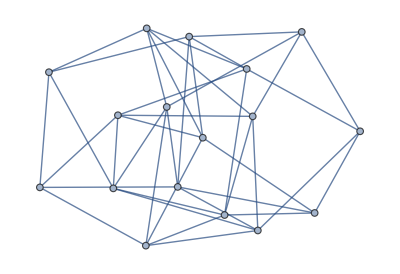
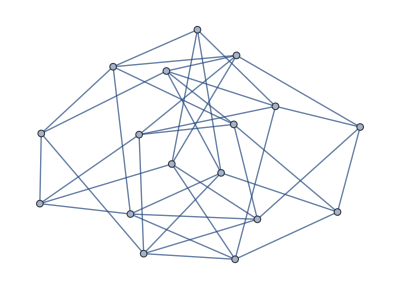
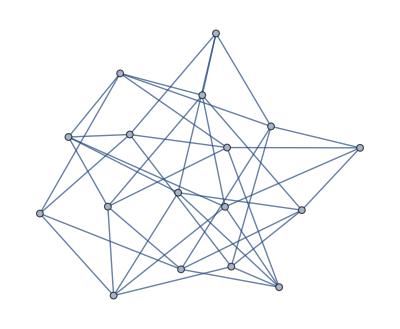
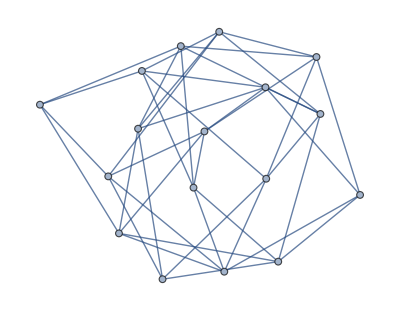
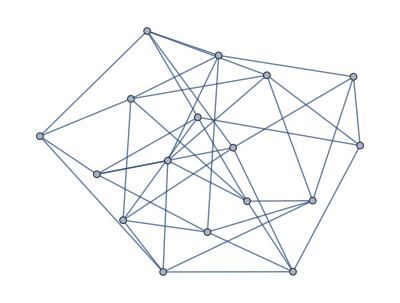
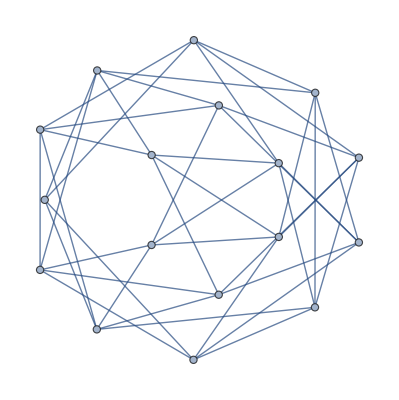
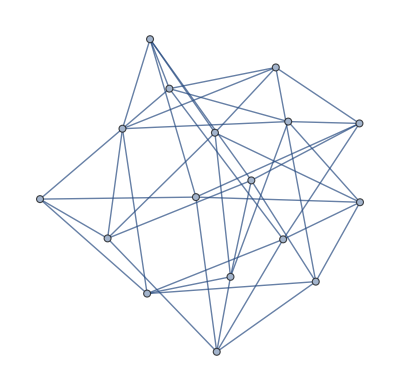

{{4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5},{4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5},{4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5}}

False

```mathematica
gl=Import["https://a-boy.github.io/playmath/stage17-Ramsey-Numbers/r36_17.g6"];
gl={gl[[3]],gl[[5]],gl[[1]],gl[[2]],gl[[4]],gl[[6]],gl[[7]]}
VertexDegree/@gl
IsomorphicGraphQ[gl[[6]],gl[[7]]]
```

```mathematica
FindHamiltonianCycle[gl[[6]],5]
```

{{1<->4,4<->10,10<->13,13<->16,16<->15,15<->9,9<->5,5<->8,8<->6,6<->2,2<->7,7<->17,17<->14,14<->11,11<->12,12<->3,3<->1},{1<->5,5<->8,8<->6,6<->2,2<->7,7<->17,17<->14,14<->11,11<->4,4<->10,10<->13,13<->16,16<->15,15<->9,9<->12,12<->3,3<->1},{1<->4,4<->10,10<->13,13<->16,16<->15,15<->9,9<->5,5<->8,8<->11,11<->14,14<->17,17<->7,7<->2,2<->6,6<->12,12<->3,3<->1},{1<->2,2<->7,7<->17,17<->14,14<->11,11<->4,4<->10,10<->13,13<->16,16<->15,15<->9,9<->5,5<->8,8<->6,6<->12,12<->3,3<->1},{1<->5,5<->8,8<->13,13<->16,16<->15,15<->9,9<->10,10<->4,4<->11,11<->14,14<->17,17<->7,7<->2,2<->6,6<->12,12<->3,3<->1}}

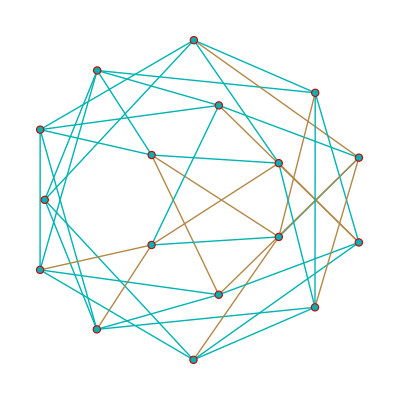

```mathematica
HighlightGraph[Graph[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17},{Null,SparseArray[Automatic,{17,17},0,{1,{{0,4,9,14,19,24,29,34,39,44,49,54,59,64,69,74,79,84},{{2},{3},{4},{5},{1},{6},{7},{14},{15},{1},{12},{13},{15},{17},{1},{10},{11},{16},{17},{1},{8},{9},{14},{16},{2},{8},{10},{12},{17},{2},{9},{11},{13},{17},{5},{6},{11},{13},{15},{5},{7},{10},{12},{15},{4},{6},{9},{13},{14},{4},{7},{8},{12},{14},{3},{6},{9},{11},{16},{3},{7},{8},{10},{16},{2},{5},{10},{11},{17},{2},{3},{8},{9},{16},{4},{5},{12},{13},{15},{3},{4},{6},{7},{14}}},Pattern}]}],%11]
```

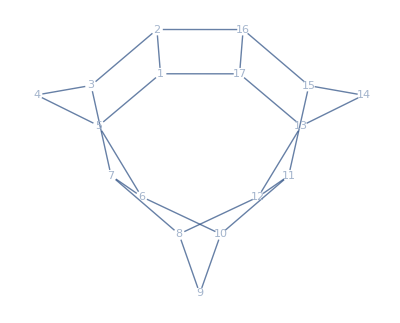
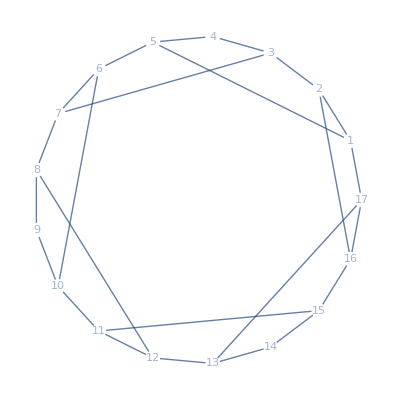

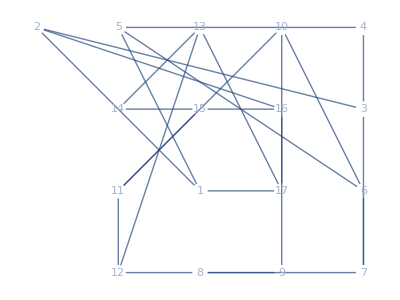
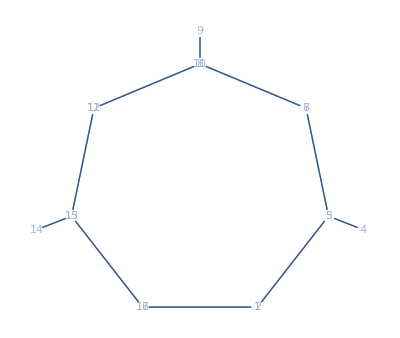
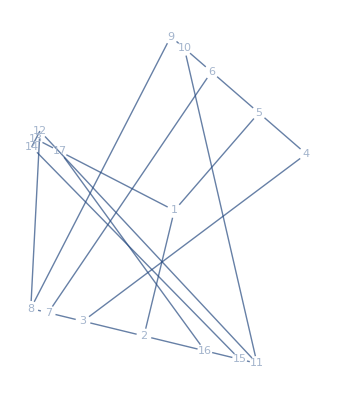
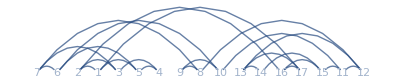
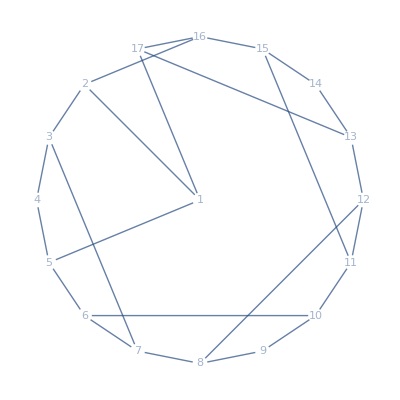
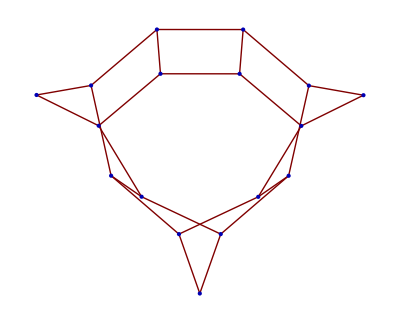

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
circleLayout[n_]:=Table[{Cos[2π/n i],Sin[2π/n i]},{i,n}];
papaya=AdjacencyGraph[{{0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1},{1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,1,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,1,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,1,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,1,0,0,1,0,0},{0,0,0,0,0,0,0,1,0,0,1,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,1,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1},{1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,0}}];
{GraphPlot[papaya,VertexShapeFunction->"Name"],GraphPlot[papaya,VertexShapeFunction->"Name",VertexCoordinates->circleLayout[17]]}
Table[GraphPlot[papaya,VertexShapeFunction->"Name",GraphLayout->layout],{layout,{"DiscreteSpiralEmbedding","HighDimensionalEmbedding","BalloonEmbedding","LinearEmbedding","StarEmbedding",}}]
```

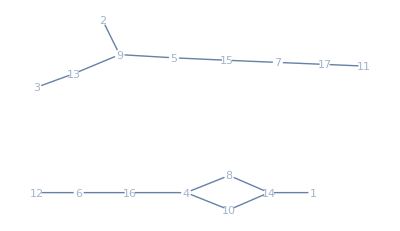
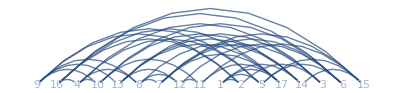
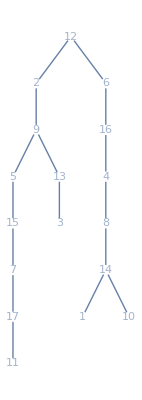
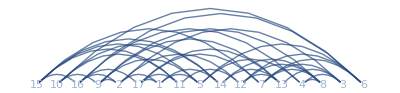
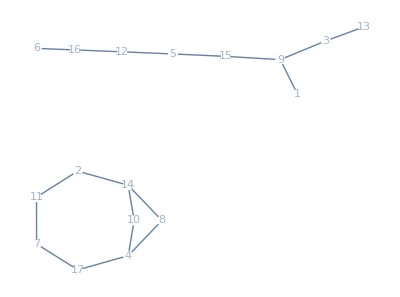
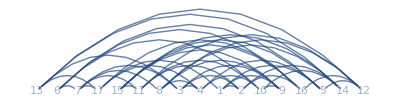
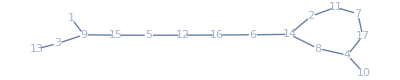
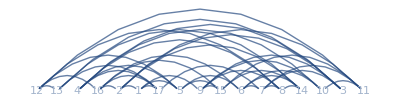
{-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-}

(0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
Table[
assoc=FindSubgraphIsomorphism[papaya,gl[[k]],1][[1]];
reverseAssoc=Association@KeyValueMap[#2->#1&,assoc];
g=Graph[EdgeList[gl[[k]]]/.reverseAssoc];
sub=FindIsomorphicSubgraph[g,papaya,1][[1]];
GraphPlot[g,VertexShapeFunction->"Name",GraphLayout->"LinearEmbedding"]+GraphPlot[sub,VertexShapeFunction->"Name"]+
GraphPlot[body=GraphDifference[g,sub],VertexShapeFunction->"Name"],
{k,7}]
AdjacencyMatrix[g]//MatrixForm
```

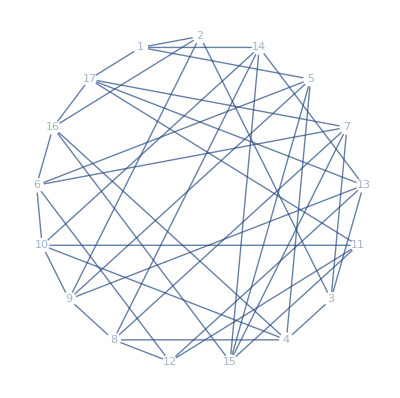
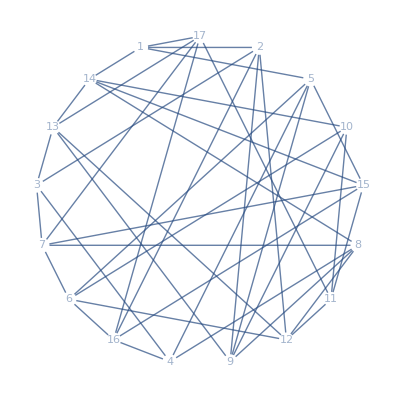
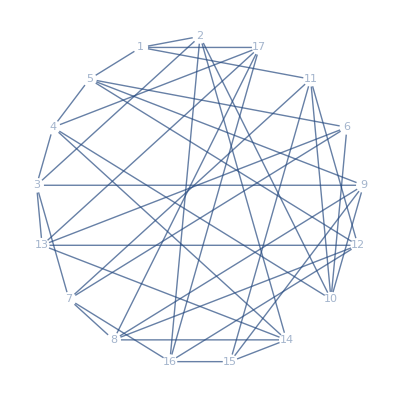
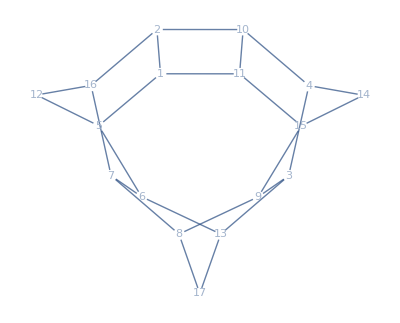
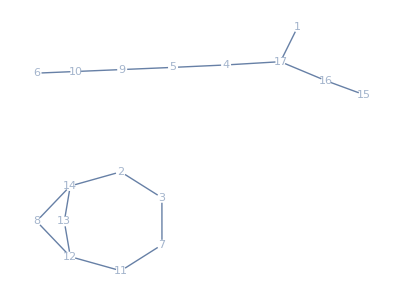
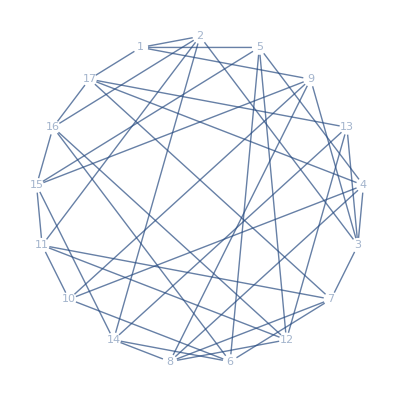
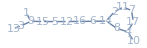
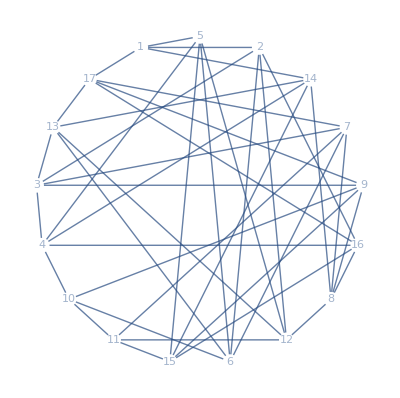
```mathematica
{-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-}
```

{-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-,-Graphics-+-Graphics-+-Graphics-}

(0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0
0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

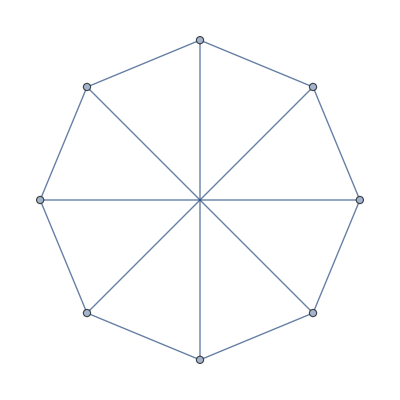

<|1→14,2→13,3→17,4→7,5→8,6→12,7→11,8→15|>

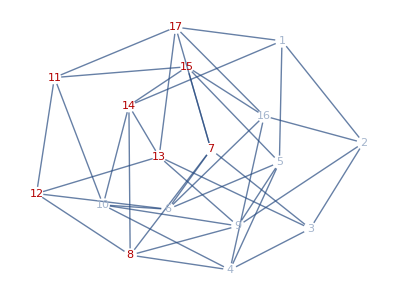

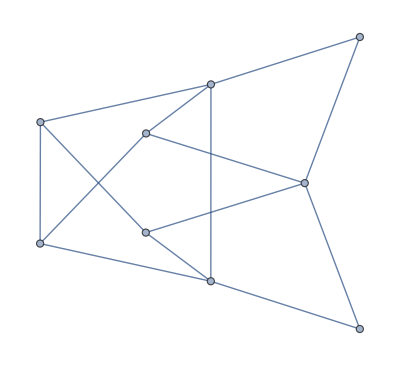

```mathematica
g8=CirculantGraph[8,{1,4}]

assoc=FindSubgraphIsomorphism[g8,gl[[1]],2][[1]]
GraphPlot[HighlightGraph[gl[[1]],Values@assoc],VertexShapeFunction->"Name"]
VertexDelete[gl[[1]],Values@assoc]
```

```mathematica
MatrixForm[m]
```

m

<|1→2,2→3,3→7,4→17,5→16,6→15,7→14,8→13,9→12,10→11,11→10,12→6,13→5,14→4,15→8,16→9|>

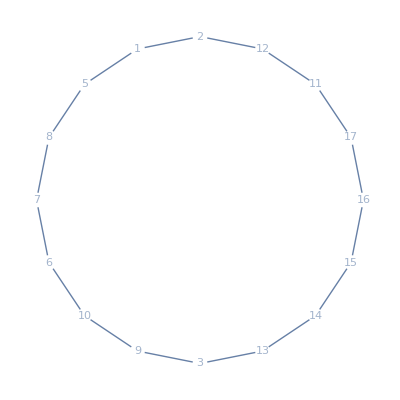

SparseArray[…]

(0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

SparseArray[…]

(0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0)

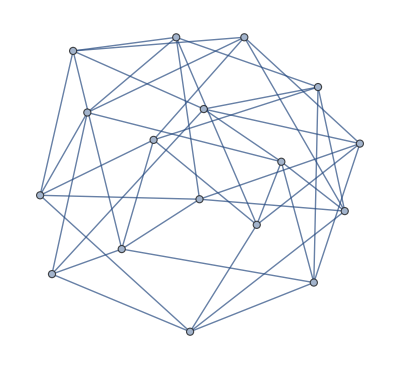

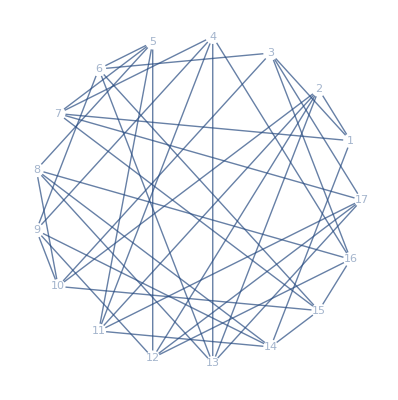

```mathematica
c16=CycleGraph[16];

assoc=FindSubgraphIsomorphism[c16,VertexDelete[gl[[6]],1],2][[1]]
(*reverseAssoc=Association@KeyValueMap[#2->#1&,assoc];
g=Graph[EdgeList[gl[[6]]]/.reverseAssoc]*)
FindIsomorphicSubgraph[g,c16,VertexShapeFunction->"Name"]
(*pm=PermutationMatrix[{1,2,3,13,14,10,4,16,17,9,8,7,6,5,15,11,12}]
ipm=pm+(IdentityMatrix[Dimensions[pm][[1]]]-DiagonalMatrix[Diagonal[pm]])
MatrixForm@ipm
Det[ipm]
m=pm.AdjacencyMatrix[gl[[6]]].pm
MatrixForm[m]*)
m=AdjacencyMatrix[gl[[6]]]
MatrixForm[m]
pm=m[[{1,2,3,13,14,10,4,16,17,9,8,7,6,5,15,11,12},{1,2,3,13,14,10,4,16,17,9,8,7,6,5,15,11,12}]]
MatrixForm[pm]
g=AdjacencyGraph[pm]
GraphPlot[g,VertexShapeFunction->"Name",VertexCoordinates->circleLayout[17]]
```